# FMM Seq. Test & Orthtree Visualization

```mathematica
<< Utility`
<< MaTeX`
SetDirectory[NBD];

r[x_]:=√(x.x)

makeBoxPoints[center_, box len_]:=With[{diagonal = ConstantArray[1,Length[center]]},
{center - (box len)/2 diagonal,center + (box len)/2 diagonal}
]

makeBox[{pt1_,pt2_}]:=With[{dim = Length[pt1]},If[dim == 2,Rectangle[pt1,pt2],Cuboid[pt1,pt2]]]
```

### Point Orthtree

```mathematica
treeGeometryData = Import["geometry.dat","Table","FieldSeparators"->","];
pointsData = Import["points.dat","Table","FieldSeparators"->","];
neighbourData = Import["neighbours.dat","Table","FieldSeparators"->","];
interactionData = Import["interactions.dat","Table","FieldSeparators"->","];

dim =  Length @ treeGeometryData[[1,4;;]];
quadtreeNodes = With[{center = #[[4;;4+dim-1]],box len = #[[3]],diag = ConstantArray[1,dim]},Join[{#[[1]],#[[2]]},Flatten[makeBoxPoints[center,box len],1] ]]&/@ treeGeometryData;

height = Max @ quadtreeNodes[[;;,2]];

quadtreeNodesbyLevel = GroupBy[quadtreeNodes,#[[2]]&];
pointsDataByNode = Association[#[[1]]->Partition[#[[2;;]],dim]&/@ pointsData] //. {}->Sequence[] ;
```

```mathematica
lpPoints = If[dim == 2, ListPlot[Values[pointsDataByNode],AspectRatio->1], 
ListPointPlot3D[Values[pointsDataByNode],AspectRatio->1]];

subdivGraphicsFun[l_]:=With[{opts =Directive[EdgeForm[Black],Opacity[0]] },
If[dim == 2, Graphics[{opts,Dynamic[Rectangle[#[[3;;3+dim-1]],#[[3+dim;;]]]&/@ quadtreeNodesbyLevel[l]]},Frame->True], Graphics3D[{opts,Dynamic[Cuboid[#[[3;;3+dim-1]],#[[3+dim;;]]]]&/@ quadtreeNodesbyLevel[l]}]]
]

interactionGraphicFun[interactionDataPoint_]:=With[{
level = interactionDataPoint[[2]],
box len = interactionDataPoint[[3]],
center = interactionDataPoint[[4;;4+dim-1]],
assocPoints = Partition[interactionDataPoint[[4+dim;;]],dim],
srcGraphicsOpts = Directive[Purple,Opacity[.25],EdgeForm[Black]],
interactsGraphicsOpts = Directive[Orange,Opacity[0.1],EdgeForm[Black]],
GraphicsFun = If[dim == 2, Graphics, Graphics3D]
},GraphicsFun@ {interactsGraphicsOpts,makeBox[makeBoxPoints[#,box len]]&/@ assocPoints,srcGraphicsOpts,makeBox[makeBoxPoints[center, box len]]}]


Manipulate[Show[{
lpPoints,
subdivGraphicsFun[l]
}],{l,0,height,1}]

Manipulate[GraphicsRow[{
Show[{subdivGraphicsFun[interactionData[[i,2]]],interactionGraphicFun @ neighbourData[[i]]}],
Show[{subdivGraphicsFun[interactionData[[i,2]]],interactionGraphicFun @ interactionData[[i]]}]
}],{i,1,Length[neighbourData],1}]
```

Show::gcomb: Could not combine the graphics objects in Show[{lpPoints,subdivGraphicsFun[3]}].

Part::partd: Part specification interactionData⟦19,2⟧ is longer than depth of object.

Part::partd: Part specification neighbourData⟦19⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{subdivGraphicsFun[interactionData⟦19,2⟧],interactionGraphicFun[neighbourData⟦19⟧]}].

Part::partd: Part specification interactionData⟦19,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{subdivGraphicsFun[interactionData⟦19,2⟧],interactionGraphicFun[interactionData⟦19⟧]}].

Part::partd: Part specification interactionData⟦19,2⟧ is longer than depth of object.

Part::partd: Part specification neighbourData⟦19⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[{subdivGraphicsFun[interactionData⟦19,2⟧],interactionGraphicFun[neighbourData⟦19⟧]}].

Part::partd: Part specification interactionData⟦19,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{subdivGraphicsFun[interactionData⟦19,2⟧],interactionGraphicFun[interactionData⟦19⟧]}].

```mathematica
n = Length @ Flatten[#,1]&@ Values[pointsDataByNode];
nLeaves = Length @ pointsData;
avgNPerLeaf = n/nLeaves //N
```

78.125

### Fmm Orthtree

```mathematica
treeGeometryData = Import["geometry.dat","Table","FieldSeparators"->","];
pointsData = Import["points.dat","Table","FieldSeparators"->","];
neighbourData = Import["neighbours.dat","Table","FieldSeparators"->","];
interactionData = Import["interactions.dat","Table","FieldSeparators"->","];

dim =  Length @ treeGeometryData[[1,4;;]];
quadtreeNodes = With[{center = #[[4;;4+dim-1]],box len = #[[3]],diag = ConstantArray[1,dim]},Join[{#[[1]],#[[2]]},Flatten[makeBoxPoints[center,box len],1] ]]&/@ treeGeometryData;

height = Max @ quadtreeNodes[[;;,2]];

quadtreeNodesbyLevel = GroupBy[quadtreeNodes,#[[2]]&];
sourceDataByNode = Association[#[[1]]->Partition[#[[2;;]],dim+1]&/@ pointsData] //. {}->Sequence[]; 
pointsDataByNode = sourceDataByNode[[;;,;;,1;;dim]];
chargeDataByNode = sourceDataByNode[[;;,;;,dim+1]];
```

```mathematica
lpPoints = If[dim == 2, ListPlot[Values[pointsDataByNode],AspectRatio->1], 
ListPointPlot3D[Values[pointsDataByNode],AspectRatio->1]];

subdivGraphicsFun[l_]:=With[{opts =Directive[EdgeForm[Black],Opacity[0]] },
If[dim == 2, Graphics[{opts,Dynamic[Rectangle[#[[3;;3+dim-1]],#[[3+dim;;]]]&/@ quadtreeNodesbyLevel[l]]},Frame->True], Graphics3D[{opts,Dynamic[Cuboid[#[[3;;3+dim-1]],#[[3+dim;;]]]]&/@ quadtreeNodesbyLevel[l]}]]
]

interactionGraphicFun[interactionDataPoint_]:=With[{
level = interactionDataPoint[[2]],
box len = interactionDataPoint[[3]],
center = interactionDataPoint[[4;;4+dim-1]],
assocPoints = Partition[interactionDataPoint[[4+dim;;]],dim],
srcGraphicsOpts = Directive[Purple,Opacity[.25],EdgeForm[Black]],
interactsGraphicsOpts = Directive[Orange,Opacity[0.1],EdgeForm[Black]],
GraphicsFun = If[dim == 2, Graphics, Graphics3D]
},GraphicsFun@ {interactsGraphicsOpts,makeBox[makeBoxPoints[#,box len]]&/@ assocPoints,srcGraphicsOpts,makeBox[makeBoxPoints[center, box len]]}]


Manipulate[Show[{
lpPoints,
subdivGraphicsFun[l]
}],{l,0,height,1}]

Manipulate[GraphicsRow[{
Show[{subdivGraphicsFun[interactionData[[i,2]]],interactionGraphicFun @ neighbourData[[i]]}],
Show[{subdivGraphicsFun[interactionData[[i,2]]],interactionGraphicFun @ interactionData[[i]]}]
}],{i,1,Length[neighbourData],1}]
```

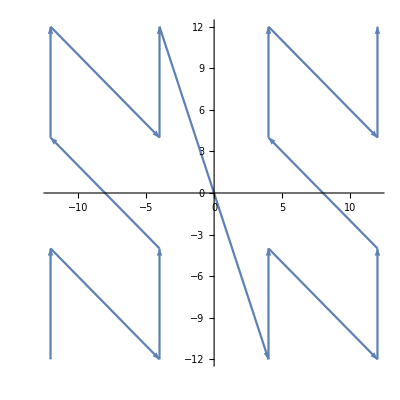

```mathematica
With[{level=2},With[{points = Mean[Partition[#,dim]]&/@quadtreeNodesbyLevel[level][[;;,3;;]]},If[dim==2,
ListPlot[points,Joined->True,PlotStyle->Arrowheads[{0,.025,0}],AspectRatio->1]/.Line[x_]:>(Arrow@Partition[x,2,1]),
Show[{ListPointPlot3D[points,PlotStyle->Arrowheads[{0,.025,0}],AspectRatio->1,AxesLabel->{"x","y","z"}],Graphics3D[{Directive[Thin,colors1[[1]],Arrowheads[{0,.015,0}]],Arrow[Partition[points,2,1]]}]}]
]] ]
```

```mathematica
Show[{subdivGraphicsFun[3],%}]
```

-Graphics-

#### Multipole Expansion test:

```mathematica
allPoints = Flatten[Values[pointsDataByNode],1];
allCharges = Flatten[Values[chargeDataByNode],1];

potFun[{x_,y_},q_,{x0_,y0_}]:=-q Log[r[{x,y}-{x0,y0}]]
forceFun[{x_,y_},q_,{x0_,y0_}]:= (q( {x,y}-{x0,y0}))/r[{x,y}-{x0,y0}]^2
```

```mathematica
potVal = NumberForm[Sum[potFun[{96,96},allCharges[[i]],allPoints[[i]]],{i,1,Length[allPoints]}],Ceiling[MachinePrecision]]
forceVal = NumberForm[Sum[forceFun[{96,96},allCharges[[i]],allPoints[[i]]],{i,1,Length[allPoints]}],Ceiling[MachinePrecision]]
```

155.0271206427696

{-0.1860250632193097,-0.1728100292067926}

#### Misc

```mathematica
n = Length @ Flatten[#,1]&@ Values[pointsDataByNode];
nLeaves = Length @ pointsData;
avgNPerLeaf = n/nLeaves //N
```

78.125

```mathematica
U[z_,z0_:0]:=-Log[z-z0]
```

```mathematica
Normal[Series[U[z,z0],{z,∞,5}]]/. {z0->(z0-p),z->(z-p)}
```

(-p+z0)/(-p+z)+(-p+z0)^2/(2 (-p+z)^2)+(-p+z0)^3/(3 (-p+z)^3)+(-p+z0)^4/(4 (-p+z)^4)+(-p+z0)^5/(5 (-p+z)^5)-Log[-p+z]

```mathematica
-Grad[q Log[r[{x,y}-{x0,y0}]],{x,y}]
```

{-(q (x-x0))/((x-x0)^2+(y-y0)^2),-(q (y-y0))/((x-x0)^2+(y-y0)^2)}

#### Binomial Lookup Table

```mathematica
genLookupTable[nmax_]:=With[{tab = Table[Binomial[n,k],{n,1,nmax},{k,1,n}]},tab]
byteSize[table_,bytes per item_:8]:=Length[Flatten[table]]*(bytes per item)/1000. (* in kB *)
```

```mathematica
nmax = 20;
byteSize[genLookupTable[nmax]]
maxVal = Max @ genLookupTable[nmax]
maxBinaryDigits = Log2[N[maxVal]]
```

1.68

184756

17.4953

```mathematica
maxLen = Max @ StringLength@ (ToString /@ Flatten @ genLookupTable[nmax]);
itemsPerLine = 80/(maxLen + 2)
```

10

```mathematica
StringRiffle[#,"\n"]&@ (StringJoin /@ Partition[StringPadRight[ToString[#]<>","& /@ Flatten @ genLookupTable[nmax]],itemsPerLine])
```

1,     2,     1,     3,     3,     1,     4,     6,     4,     1,     
5,     10,    10,    5,     1,     6,     15,    20,    15,    6,     
1,     7,     21,    35,    35,    21,    7,     1,     8,     28,    
56,    70,    56,    28,    8,     1,     9,     36,    84,    126,   
126,   84,    36,    9,     1,     10,    45,    120,   210,   252,   
210,   120,   45,    10,    1,     11,    55,    165,   330,   462,   
462,   330,   165,   55,    11,    1,     12,    66,    220,   495,   
792,   924,   792,   495,   220,   66,    12,    1,     13,    78,    
286,   715,   1287,  1716,  1716,  1287,  715,   286,   78,    13,    
1,     14,    91,    364,   1001,  2002,  3003,  3432,  3003,  2002,  
1001,  364,   91,    14,    1,     15,    105,   455,   1365,  3003,  
5005,  6435,  6435,  5005,  3003,  1365,  455,   105,   15,    1,     
16,    120,   560,   1820,  4368,  8008,  11440, 12870, 11440, 8008,  
4368,  1820,  560,   120,   16,    1,     17,    136,   680,   2380,  
6188,  12376, 19448, 24310, 24310, 19448, 12376, 6188,  2380,  680,   
136,   17,    1,     18,    153,   816,   3060,  8568,  18564, 31824, 
43758, 48620, 43758, 31824, 18564, 8568,  3060,  816,   153,   18,    
1,     19,    171,   969,   3876,  11628, 27132, 50388, 75582, 92378, 
92378, 75582, 50388, 27132, 11628, 3876,  969,   171,   19,    1,     
20,    190,   1140,  4845,  15504, 38760, 77520, 125970,167960,184756,
167960,125970,77520, 38760, 15504, 4845,  1140,  190,   20,    1,